Basic analysis of dumps captured from Android battery  ”uevent” interface

Phillip Stanley-Marbell
phillip.stanleymarbell@gmail.com / psm@mit.edu

February 2016

```mathematica
SetDirectory[NotebookDirectory[]];

analyze[deviceFamily_, fileName_] := Module[{grepCurrentBeforeCount,grepVoltageBeforeCount, currentGroupSize, voltageGroupSize,currentIndex,voltageIndex,
rawCurrents,rawVoltages,rawCurrentsGrouped,rawVoltagesGrouped,datesAndCurrentsMicroamps,datesAndDischargeCurrentsMicroamps,datesAndDischargeCurrentsAbsoluteMicroamps,datesAndVoltageMicrovolts, datesAndPowerMilliwatts},

grepCurrentBeforeCount = If[deviceFamily == "nexus6p",
	15,
(* Else *)
	11];

grepVoltageBeforeCount = If[deviceFamily == "nexus6p",
	17,
(* Else *)
	9];

currentGroupSize = grepCurrentBeforeCount+2;

voltageGroupSize =grepVoltageBeforeCount + 2;

currentIndex = If[deviceFamily == "nexus6p",
	16,
(* Else *)
	12];

voltageIndex = If[deviceFamily == "nexus6p",
	18,
(* Else *)
	10];


rawCurrents =Import["!grep -B "<>ToString[grepCurrentBeforeCount]<>" 'POWER_SUPPLY_CURRENT_NOW' "<>fileName, "List"];
rawCurrentsGrouped = Partition[rawCurrents, currentGroupSize];(*Print[rawGrouped];*)
datesAndCurrentsMicroamps= {DateObject[#[[1]]], ToExpression[StringSplit[#[[currentIndex]], "="][[2]]]}&/@rawCurrentsGrouped;
datesAndDischargeCurrentsMicroamps = {#[[1]], Abs[#[[2]]]}&/@datesAndCurrentsMicroamps;(*Select[datesAndCurrentsMicroamps, #[[2]]≤ 0&];*)
datesAndDischargeCurrentsAbsoluteMicroamps = {#[[1]], Abs[#[[2]]]/10^3}&/@ datesAndDischargeCurrentsMicroamps;


rawVoltages =Import["!grep -B "<>ToString[grepVoltageBeforeCount]<>" 'POWER_SUPPLY_VOLTAGE_NOW' "<>fileName, "List"];
rawVoltagesGrouped = Partition[rawVoltages, voltageGroupSize];
datesAndVoltageMicrovolts= {DateObject[#[[1]]], ToExpression[StringSplit[#[[voltageIndex]], "="][[2]]]/10^6}&/@rawVoltagesGrouped;


datesAndPowerMilliwatts = Table[{datesAndDischargeCurrentsAbsoluteMicroamps[[i]][[1]], datesAndDischargeCurrentsAbsoluteMicroamps[[i]][[2]]*datesAndVoltageMicrovolts[[i]][[2]]}, {i, 1, Length[datesAndDischargeCurrentsAbsoluteMicroamps]}];


Column[{DateListPlot[datesAndDischargeCurrentsAbsoluteMicroamps,
AspectRatio->1/3,
PlotTheme->"Detailed",
ImageSize->800,
Frame->True,
InterpolationOrder->0,
GridLines->{Automatic,None},
PlotStyle->{FontSize-> 18},
FrameLabel->{"Time", "Sampled Battery Current (mA)"},
FrameStyle->{{Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Gray, Thickness[0.001]], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, LightGray]}, {Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Black, Thick], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, GrayLevel[0.45], Thickness[0.0035]]}}],
DateListLogPlot[datesAndDischargeCurrentsAbsoluteMicroamps,
AspectRatio->1/3,
PlotTheme->"Detailed",
ImageSize->800,
Frame->True,
InterpolationOrder->0,
GridLines->{Automatic,None},
PlotStyle->{FontSize-> 18},
FrameLabel->{"Time", "Sampled Battery Current (mA)"},
FrameStyle->{{Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Gray, Thickness[0.001]], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, LightGray]}, {Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Black, Thick], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, GrayLevel[0.45], Thickness[0.0035]]}}],


DateListPlot[datesAndVoltageMicrovolts,
AspectRatio->1/3,
PlotRange->{0, 4.6},
PlotTheme->"Detailed",
ImageSize->800,
Frame->True,
InterpolationOrder->0,
GridLines->{Automatic,None},
PlotStyle->{FontSize-> 18},
FrameLabel->{"Time", "Sampled Battery Voltage (Volts)"},
FrameStyle->{{Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Gray, Thickness[0.001]], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, LightGray]}, {Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Black, Thick], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, GrayLevel[0.45], Thickness[0.0035]]}}],

DateListLogPlot[datesAndVoltageMicrovolts,
AspectRatio->1/3,
PlotRange->{0.1, 10},
PlotTheme->"Detailed",
ImageSize->800,
Frame->True,
InterpolationOrder->0,
GridLines->{Automatic,None},
PlotStyle->{FontSize-> 18},
FrameLabel->{"Time", "Sampled Battery Voltage (Volts)"},
FrameStyle->{{Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Gray, Thickness[0.001]], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, LightGray]}, {Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Black, Thick], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, GrayLevel[0.45], Thickness[0.0035]]}}],


DateListPlot[datesAndPowerMilliwatts,
AspectRatio->1/3,
PlotTheme->"Detailed",
ImageSize->800,
Frame->True,
InterpolationOrder->0,
GridLines->{Automatic,None},
PlotStyle->{FontSize-> 18},
FrameLabel->{"Time", "Power Drain (mW)"},
FrameStyle->{{Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Gray, Thickness[0.001]], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, LightGray]}, {Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Black, Thick], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, GrayLevel[0.45], Thickness[0.0035]]}}],

DateListLogPlot[datesAndPowerMilliwatts,
AspectRatio->1/3,
PlotTheme->"Detailed",
ImageSize->800,
Frame->True,
InterpolationOrder->0,
GridLines->{Automatic,None},
PlotStyle->{FontSize-> 18},
FrameLabel->{"Time", "Power Drain (mW)"},
FrameStyle->{{Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Gray, Thickness[0.001]], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, LightGray]}, {Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Black, Thick], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, GrayLevel[0.45], Thickness[0.0035]]}}]
}]
];
```

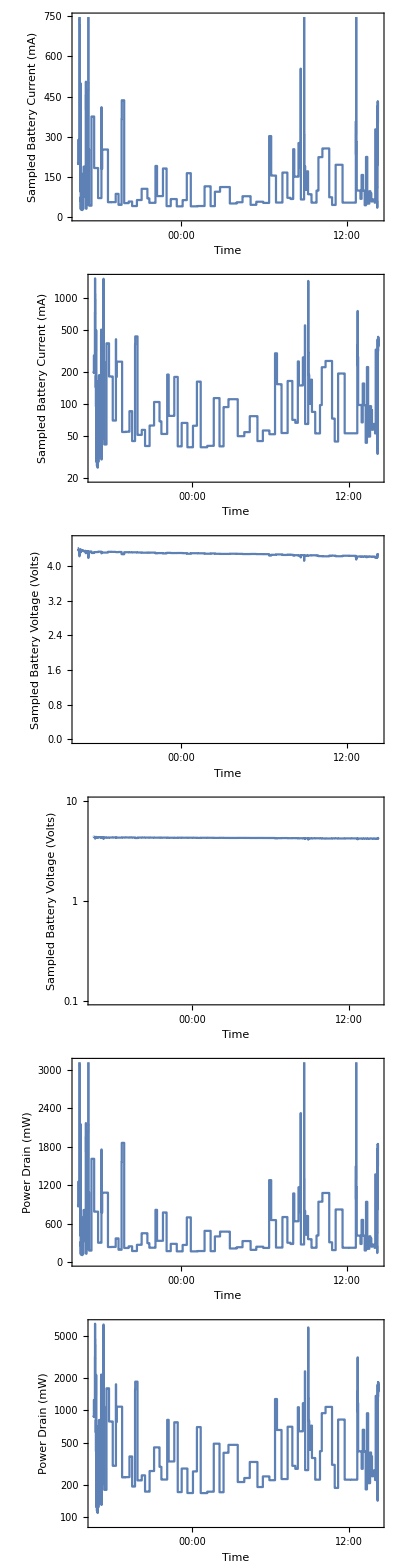

```mathematica
analyze["nexus6p", "../Logs/2016-02-03-14-15-47.txt"]
```